# Rabi vs Trans

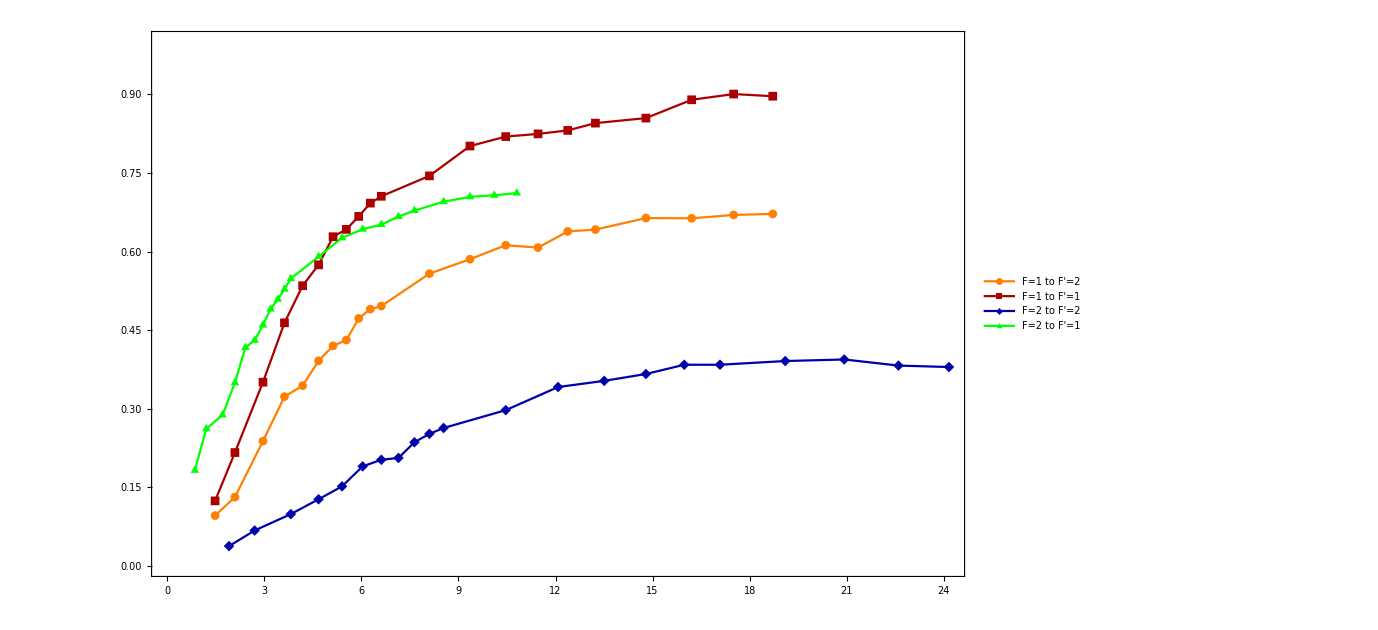

```mathematica
dd1=ListPlot[{Transpose[{Rabi8722[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8711,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{Rabi8721[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8712,4]]/Log[Mean/@Partition[EITmin8712,4]]}],Transpose[{Rabi8712[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8721,4]]/Log[Mean/@Partition[EITmin8721,4]]}],Transpose[{Rabi8711[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8722,4]]/Log[Mean/@Partition[EITmin8722,4]]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=2","F=2 to F'=1"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Darker[Blue],Green},PlotStyle->{Orange, Darker[Red],Darker[Blue],Green},Frame->True]
```

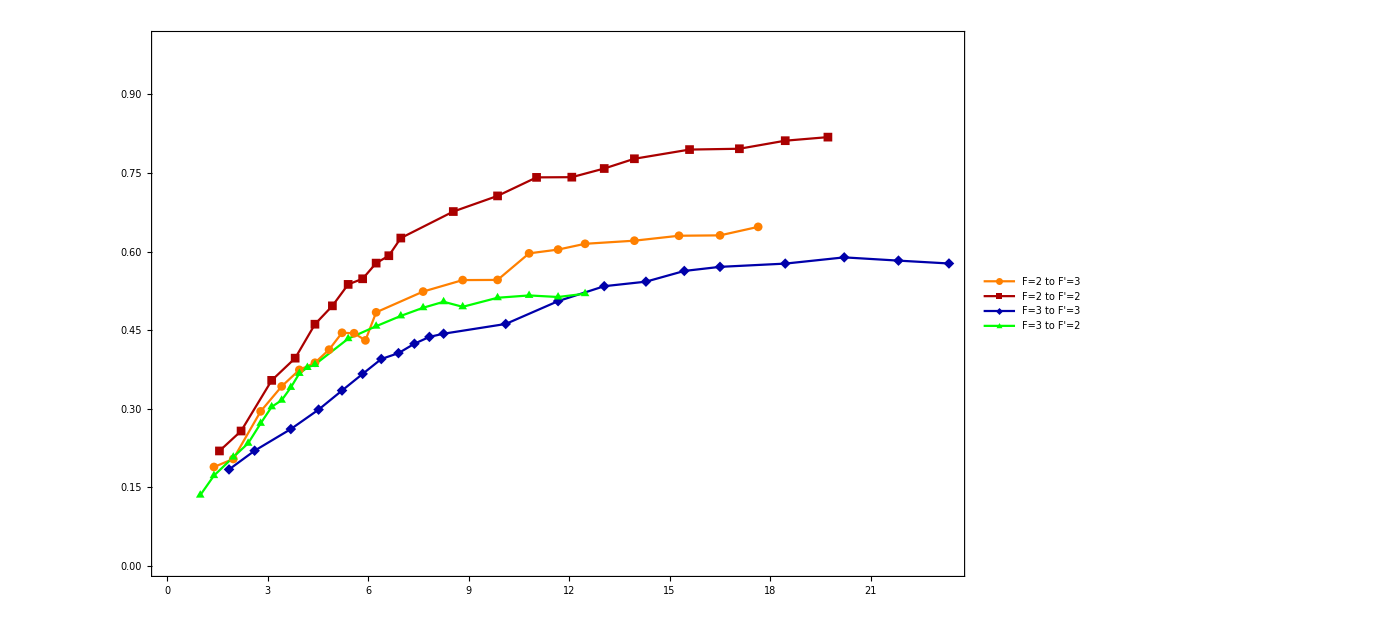

```mathematica
dd=ListPlot[{Transpose[{Rabi8522[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7711,4]]/Log[Mean/@Partition[EITmin7711,4]]}],Transpose[{Rabi8521[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7712,4]]/Log[Mean/@Partition[EITmin7712,4]]}],Transpose[{Rabi8512[pw/1000,0.9/1000],1-EITmax7721L/EITmin7721L}],Transpose[{Rabi8511[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7722,4]]/Log[Mean/@Partition[EITmin7722,4]]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=2 to F'=3","F=2 to F'=2","F=3 to F'=3","F=3 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Darker[Blue],Green},PlotStyle->{Orange, Darker[Red],Darker[Blue],Green},Frame->True]
```

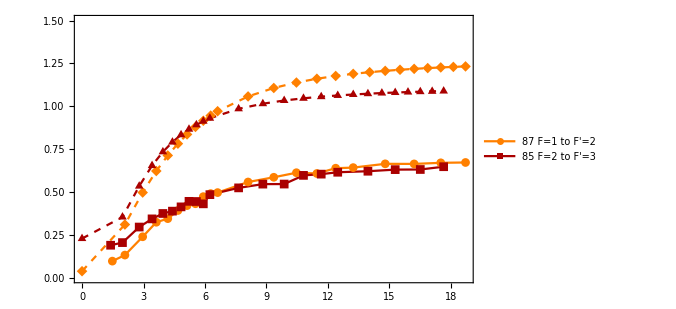

```mathematica
a1=ListPlot[{Transpose[{Rabi8722[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8711,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{Rabi8522[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7711,4]]/Log[Mean/@Partition[EITmin7711,4]]}],Tvw8722,Tvw8522},PlotRange->{0,1.5},ImageSize->500,PlotRange->{0,0.8},PlotLegends->{"87 F=1 to F'=2","85 F=2 to F'=3"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

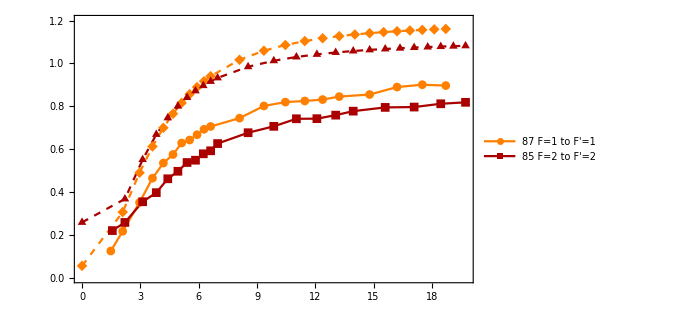

```mathematica
a2=ListPlot[{Transpose[{Rabi8721[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8712,4]]/Log[Mean/@Partition[EITmin8712,4]]}],Transpose[{Rabi8521[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7712,4]]/Log[Mean/@Partition[EITmin7712,4]]}],Tvw8721,Tvw8521},PlotRange->{0,1.2},ImageSize->500,PlotRange->{0,0.8},PlotLegends->{"87 F=1 to F'=1","85 F=2 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

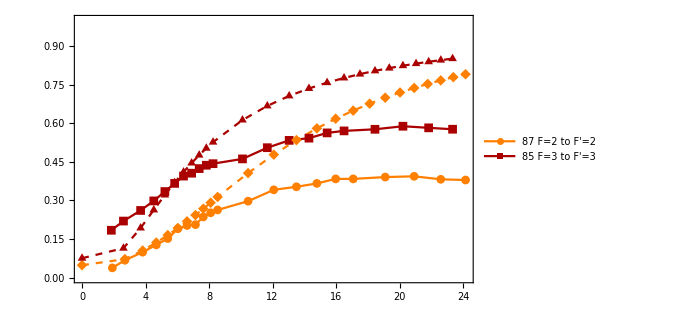

```mathematica
a3=ListPlot[{Transpose[{Rabi8712[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8721,4]]/Log[Mean/@Partition[EITmin8721,4]]}],Transpose[{Rabi8512[pw/1000,0.9/1000],1-EITmax7721L/EITmin7721L}],Tvw8712,Tvw8512},PlotRange->{0,1},ImageSize->500,PlotRange->{0,0.8},PlotLegends->{"87 F=2 to F'=2","85 F=3 to F'=3"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

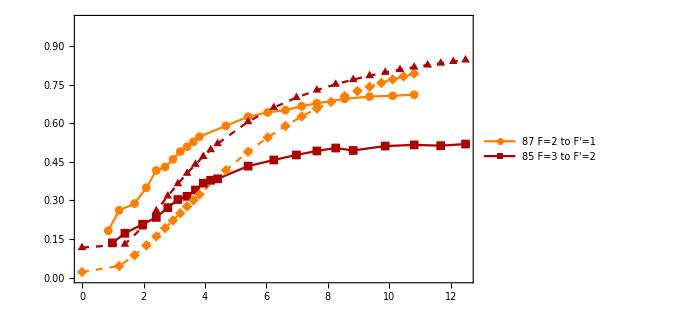

```mathematica
a4=ListPlot[{Transpose[{Rabi8711[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax8722,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{Rabi8511[pw/1000,0.9/1000],1-Log[Mean/@Partition[EITmax7722,4]]/Log[Mean/@Partition[EITmin7722,4]]}],Tvw8711,Tvw8511},PlotRange->{0,1},ImageSize->500,PlotRange->{0,0.8},PlotLegends->{"87 F=2 to F'=1","85 F=3 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

```mathematica
GraphicsGrid[{{a1,a2},{a3,a4}},ImageSize->1400,AspectRatio->0.5]
```

-Graphics-

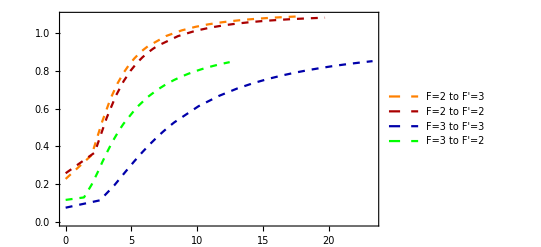

```mathematica
tr=ListPlot[{Tvw8522,Tvw8521,Tvw8512,Tvw8511},Joined->True,PlotLegends->{"F=2 to F'=3","F=2 to F'=2","F=3 to F'=3","F=3 to F'=2"},Joined->True,PlotStyle->{{Dashed,Orange}, {Dashed,Darker[Red]},{Dashed,Darker[Blue]},{Dashed,Green}},Frame->True]
```

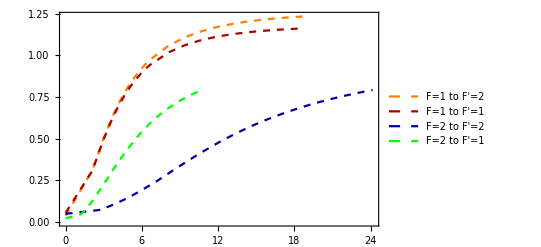

```mathematica
tr1=ListPlot[{Tvw8722,Tvw8721,Tvw8712,Tvw8711},Joined->True,PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=2","F=2 to F'=1"},Joined->True,PlotStyle->{{Dashed,Orange}, {Dashed,Darker[Red]},{Dashed,Darker[Blue]},{Dashed,Green}},Frame->True]
```

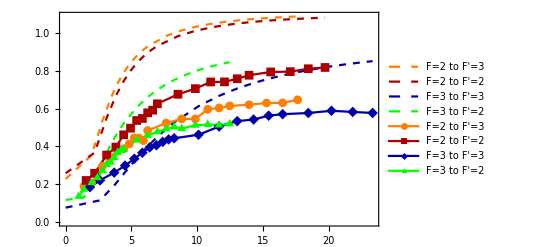

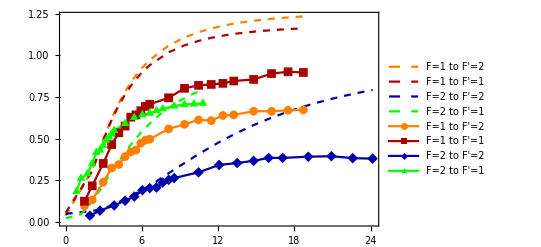

```mathematica
Show[tr,dd]
Show[tr1,dd1]
```

# Power vs Trans

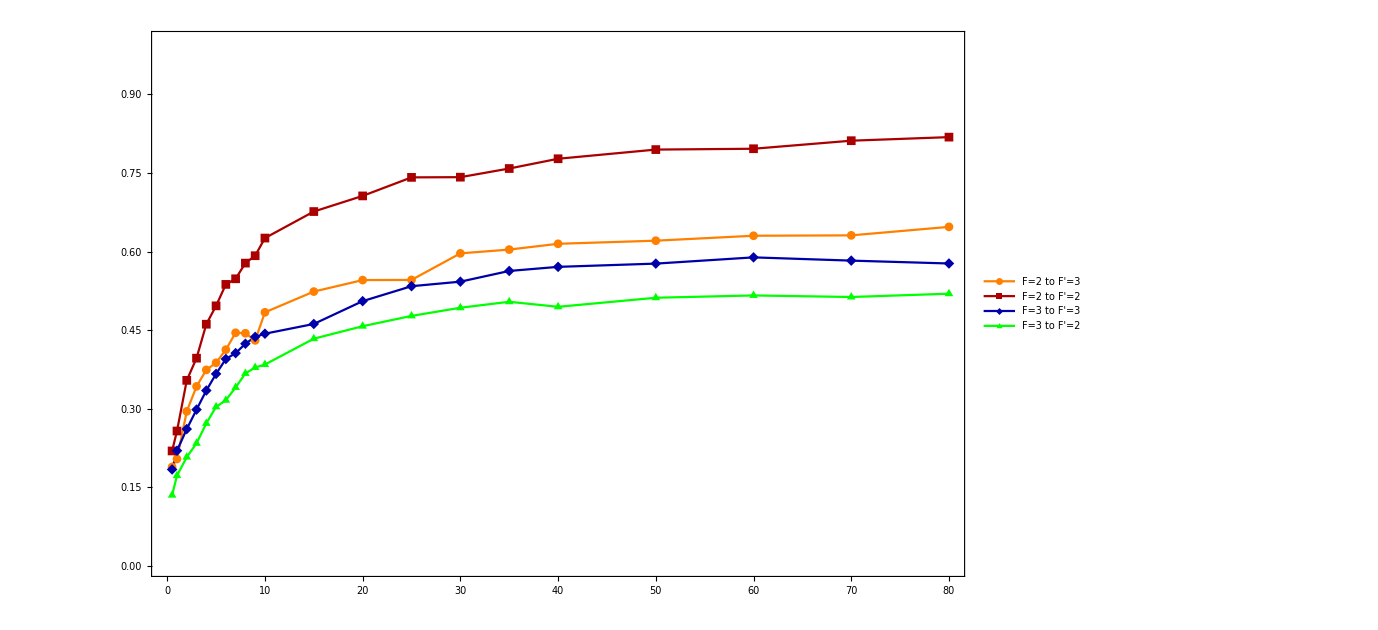

```mathematica
ddL=ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax7711,4]]/Log[Mean/@Partition[EITmin7711,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax7712,4]]/Log[Mean/@Partition[EITmin7712,4]]}],Transpose[{pw,1-EITmax7721L/EITmin7721L}],Transpose[{pw,1-Log[Mean/@Partition[EITmax7722,4]]/Log[Mean/@Partition[EITmin7722,4]]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=2 to F'=3","F=2 to F'=2","F=3 to F'=3","F=3 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Darker[Blue],Green},PlotStyle->{Orange, Darker[Red],Darker[Blue],Green},Frame->True]
```

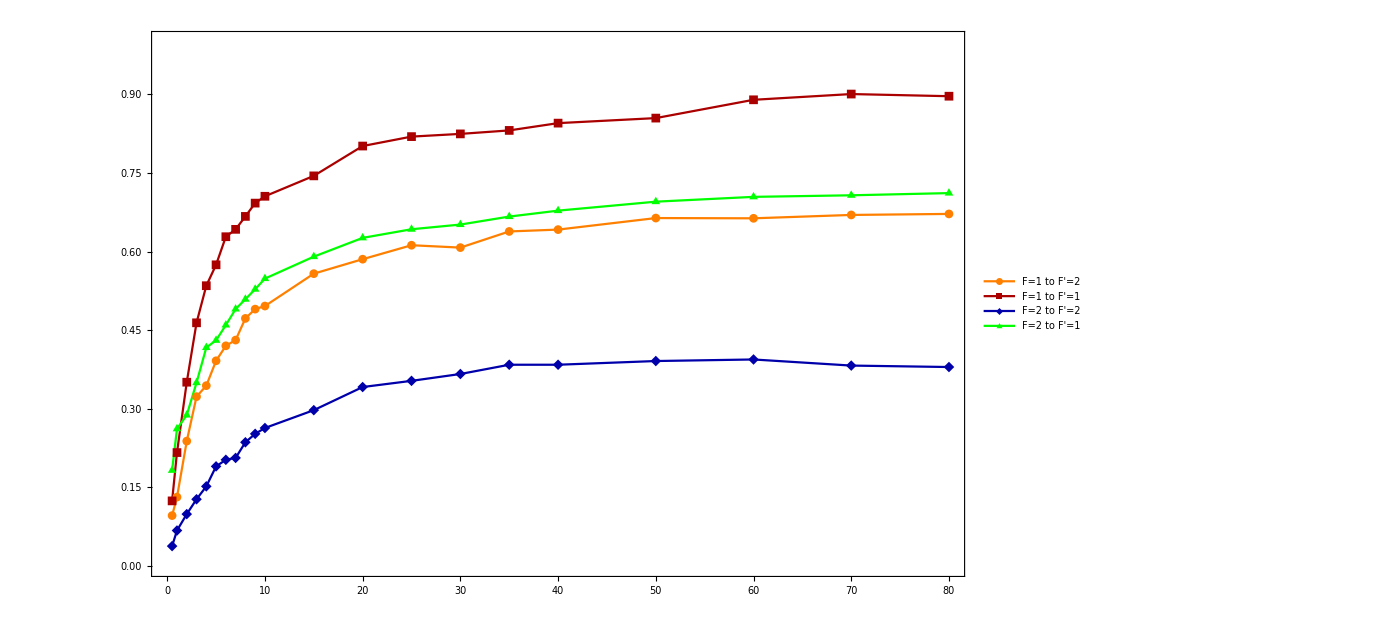

```mathematica
dd1L=ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax8711,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax8712,4]]/Log[Mean/@Partition[EITmin8712,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax8721,4]]/Log[Mean/@Partition[EITmin8721,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax8722,4]]/Log[Mean/@Partition[EITmin8722,4]]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=2","F=2 to F'=1"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],Darker[Blue],Green},PlotStyle->{Orange, Darker[Red],Darker[Blue],Green},Frame->True]
```

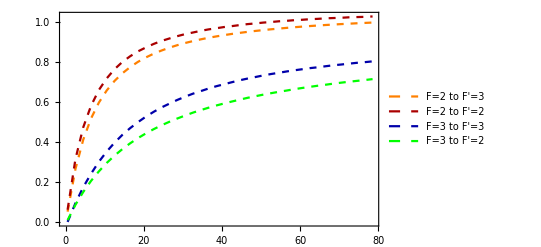

```mathematica
trL=ListPlot[{Tvw8522,Tvw8521,Tvw8512,Tvw8511},Joined->True,PlotLegends->{"F=2 to F'=3","F=2 to F'=2","F=3 to F'=3","F=3 to F'=2"},Joined->True,PlotStyle->{{Dashed,Orange}, {Dashed,Darker[Red]},{Dashed,Darker[Blue]},{Dashed,Green}},Frame->True]
```

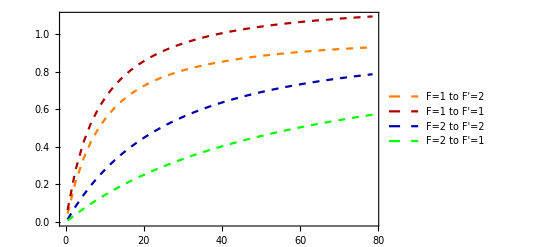

```mathematica
tr1L=ListPlot[{Tvw8722,Tvw8721,Tvw8712,Tvw8711},Joined->True,PlotLegends->{"F=1 to F'=2","F=1 to F'=1","F=2 to F'=2","F=2 to F'=1"},Joined->True,PlotStyle->{{Dashed,Orange}, {Dashed,Darker[Red]},{Dashed,Darker[Blue]},{Dashed,Green}},Frame->True]
```

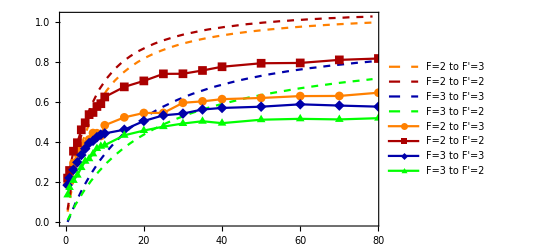

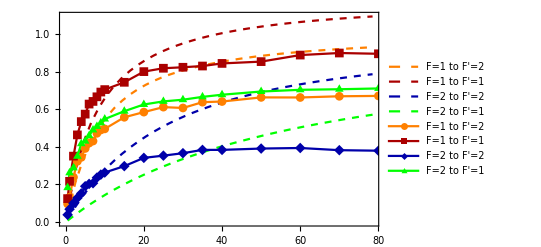

```mathematica
Show[trL,ddL]
Show[tr1L,dd1L]
```

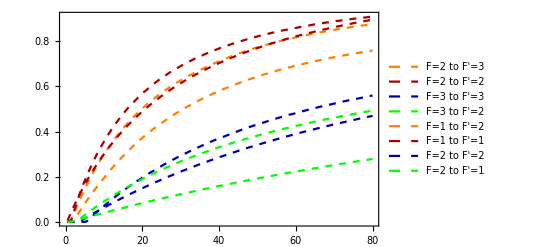

```mathematica
Show[trL,tr1L]
```

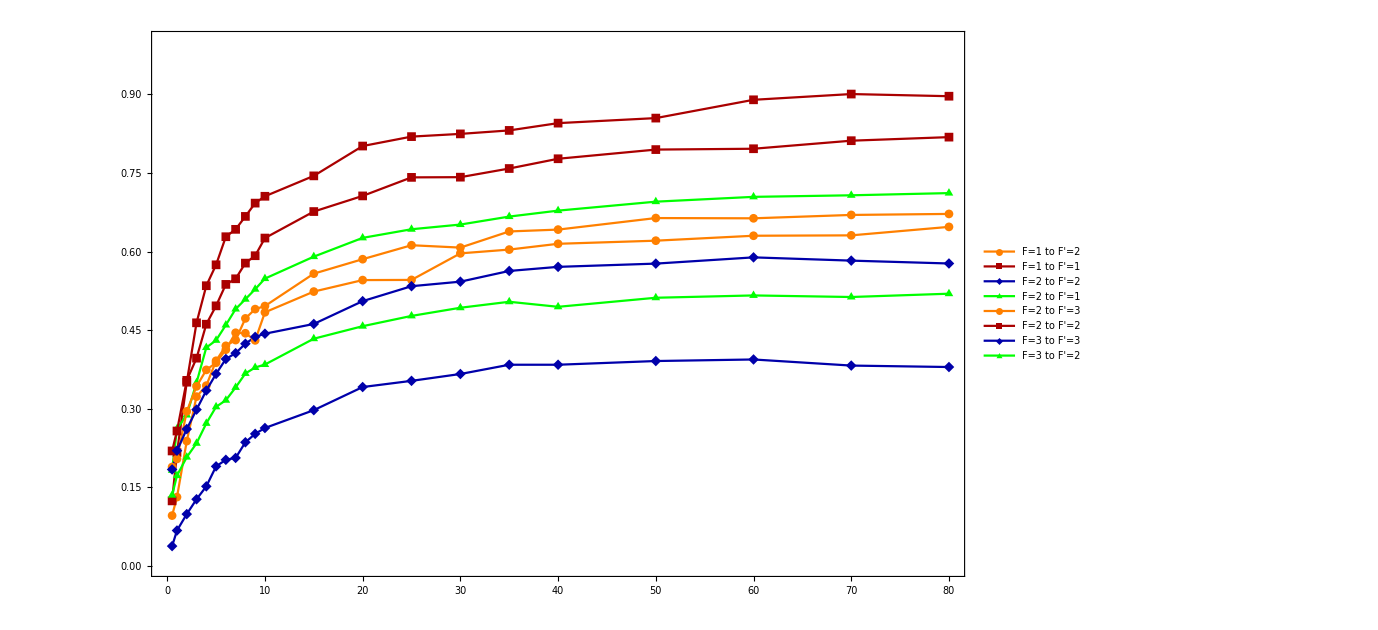

```mathematica
Show[dd1L,ddL]
```

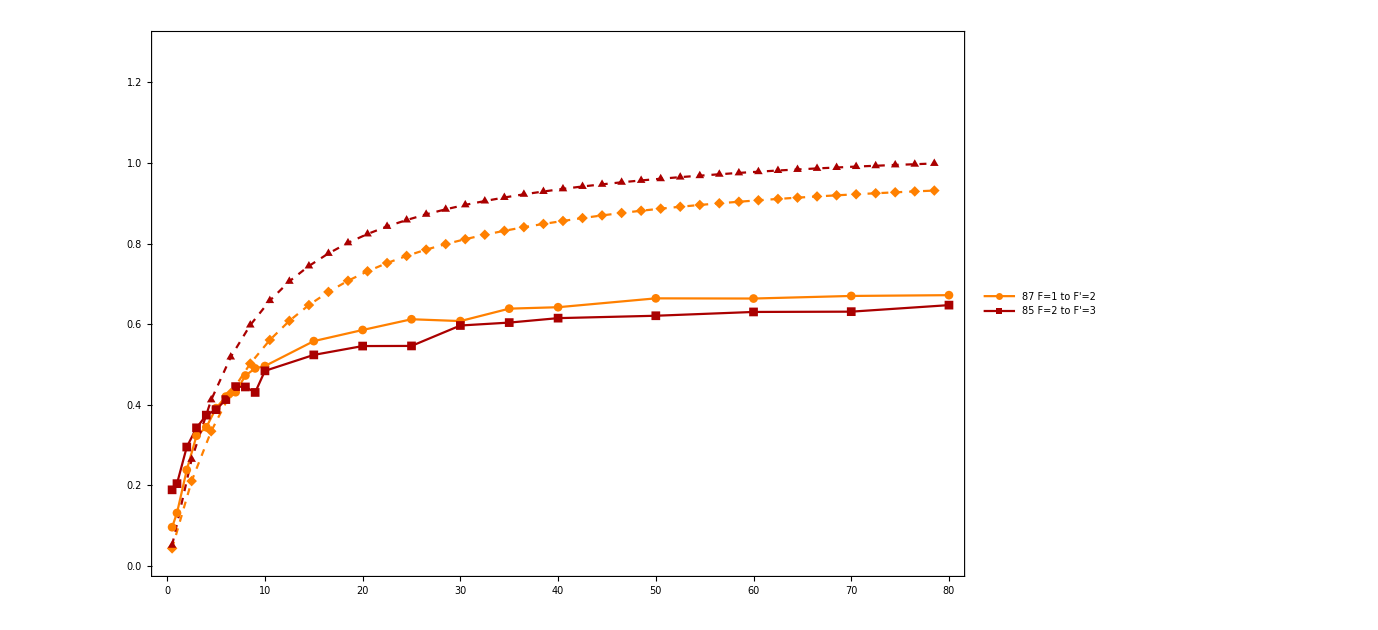

```mathematica
ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax8711,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax7711,4]]/Log[Mean/@Partition[EITmin7711,4]]}],Tvw8722,Tvw8522},PlotRange->{0,1.3},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"87 F=1 to F'=2","85 F=2 to F'=3"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

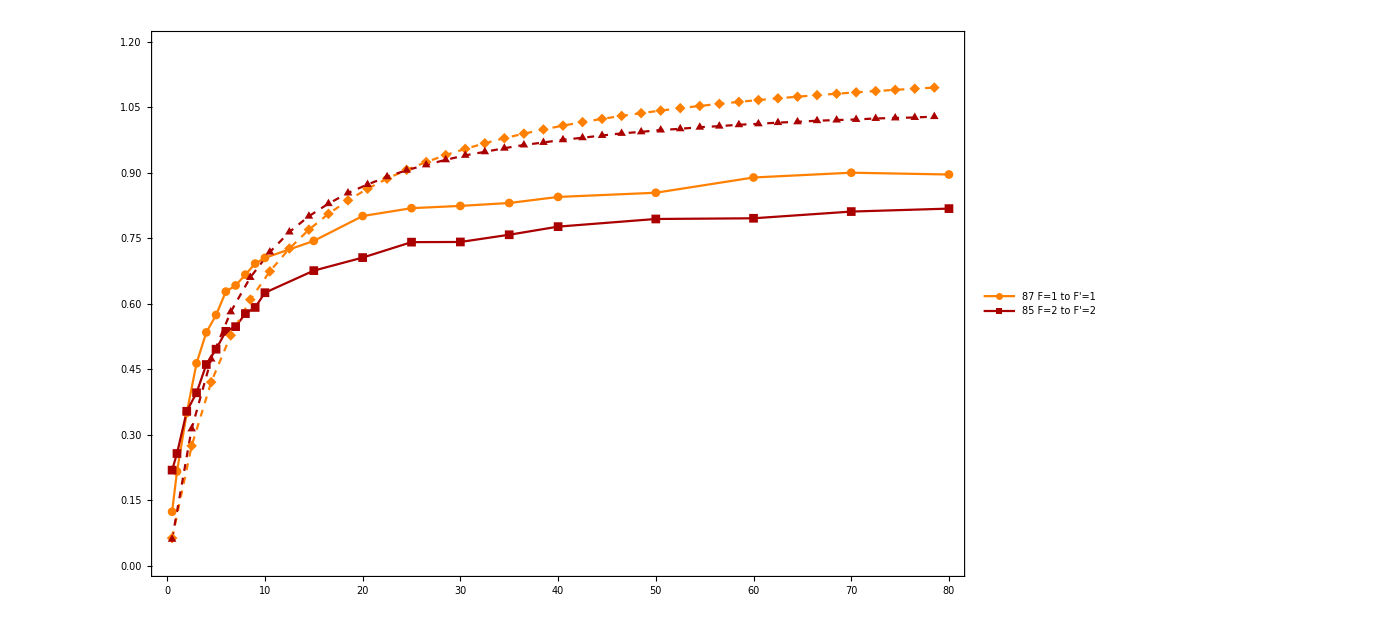

```mathematica
ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax8712,4]]/Log[Mean/@Partition[EITmin8712,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax7712,4]]/Log[Mean/@Partition[EITmin7712,4]]}],Tvw8721,Tvw8521},PlotRange->{0,1.2},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"87 F=1 to F'=1","85 F=2 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

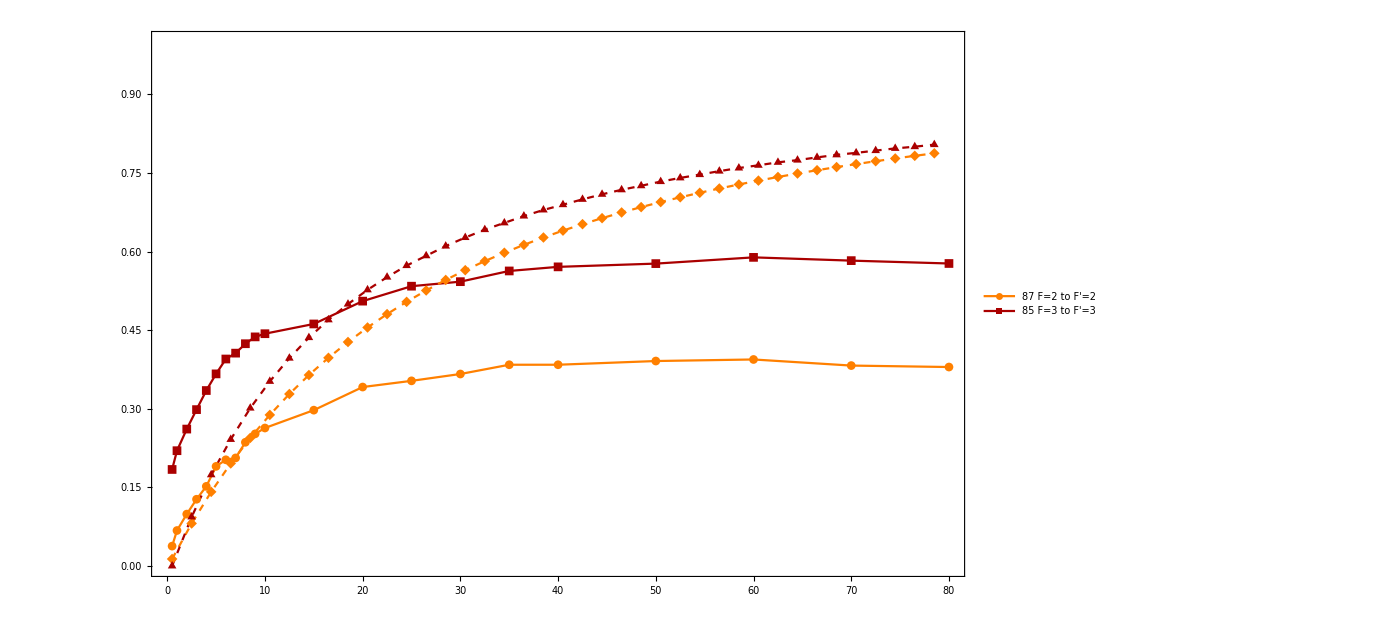

```mathematica
ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax8721,4]]/Log[Mean/@Partition[EITmin8721,4]]}],Transpose[{pw,1-EITmax7721L/EITmin7721L}],Tvw8712,Tvw8512},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"87 F=2 to F'=2","85 F=3 to F'=3"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```

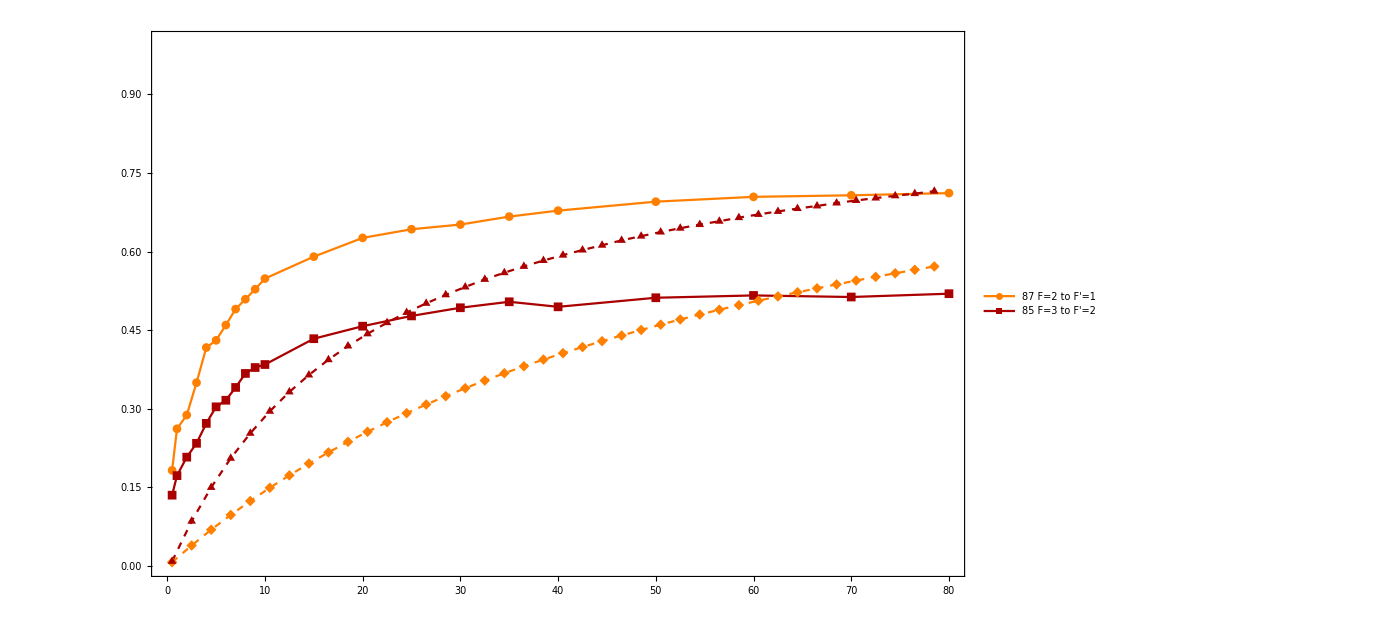

```mathematica
ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax8722,4]]/Log[Mean/@Partition[EITmin8722,4]]}],Transpose[{pw,1-Log[Mean/@Partition[EITmax7722,4]]/Log[Mean/@Partition[EITmin7722,4]]}],Tvw8711,Tvw8511},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8},PlotLegends->{"87 F=2 to F'=1","85 F=3 to F'=2"},Joined->True,PlotMarkers->Automatic,MeshStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},PlotStyle->{Orange, Darker[Red],{Orange,Dashed},{ Darker[Red],Dashed}},Frame->True]
```